# Test Dirac NDF C++ implementation

## License

/*
 * Copyright (c) <2023> NVIDIA CORPORATION & AFFILIATES. All rights reserved.
 *
 * Licensed under the Apache License, Version 2.0 (the “License”);
 * you may not use this file except in compliance with the License.
 * You may obtain a copy of the License at
 *
 *     http://www.apache.org/licenses/LICENSE-2.0
 *
 * Unless required by applicable law or agreed to in writing, software
 * distributed under the License is distributed on an “AS IS” BASIS,
 * WITHOUT WARRANTIES OR CONDITIONS OF ANY KIND, either express or implied.
 * See the License for the specific language governing permissions and
 * limitations under the License.
 */

```mathematica
Run["clang++ -I include test/NDFs/test_dirac_NDF_sigma.cpp -O3 -o test/NDFs/test_dirac_NDF_sigma"]
```

0

```mathematica
plotpoints[data_,d_,min_]:=Table[{min+d i - 0.5 d,data[[i]]},{i,1,Length[data]}];
```

```mathematica
Dirac`σ[u_,ui_]:=Re[2(√(1-u^2-ui^2)+u ui ArcCos[-(u ui)/(√(1-u^2) √(1-ui^2))])]
```

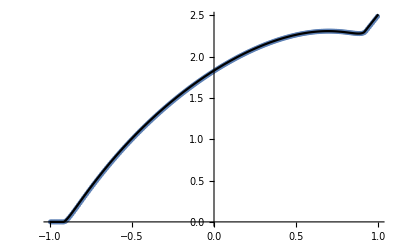

```mathematica
un=.4;
Run["./test/NDFs/test_dirac_NDF_sigma 0.01 "<>ToString[un]<>" > test.txt"];
p=Import["test.txt","Table"];
Show[
ListPlot[plotpoints[p[[1]],0.01,-1]],
Plot[Dirac`σ[u,un],{u,-1,1},PlotStyle->Black]
]
```